# “Accurate determination of spectra in discrete-time quantum mechanics”

### Obliczenia analityczne

(1) ⅈ∂_t ψ=Hψ - równanie Schrodingera zależne od czasu
(2) Eψ=Hψ - równanie na wartości własne operatora energii
artykuł Bender et al. proponuje metodę numeryczną rozwiązywania równania (2)
Piecewise[{{∂_t q̂=p̂, ewolucja położenia}, {∂_t p̂=-V'(q̂), ewolucja pędu}}]
mechanika kwantowa nakłada warunek [q̂(t),p̂(t)]=ⅈ
Piecewise[{{q(t+Δt)=q(t)+Δtp(t), □}, {p(t+Δt)=p(t)+ΔtV'(t), □}}]
powyższe równania nie spełniają warunku komutacji, jednak wystarczy zmienić równania:
Piecewise[{{q(t)≃q(nΔt)=q_n, □}, {p(t)≃p(nΔt)=p_n, □}}]
otrzymujemy wtedy równania:
Piecewise[{{q_(n+1)=q_n+hp_n-h^2/2 V'(q_n), □}, {p_(n+1)=q_n-h/2[V'(q_n)+V'(q_(n+1))], □}}]
przypis (5) w pracy pokazuje, jak znaleźć energie własne w bazie oscylatora harmonicznego:
w wyniku transformaty Fouriera otrzymujemy różnice energii własnych dla szukanego problemu

### Parametry symulacji

```mathematica
ClearAll["Global `*"];  (* czyszczenie jądra programu ze wszystkich zmiennych *)
```

```mathematica
dmax=11; (* wymiar przestrzeni *)
nmax=2^9; (* liczba kroków czasowych -> szybka transformata Fouriera *)
h=0.1; (* krok różniczkowania numerycznego *)
g=0.885;  (* parametr potencjału V(q)=gq^4 *)
```

### Macierze początkowe położenia i pędu

```mathematica
$PrePrint=MatrixForm; (* wyświetlanie w formie macierzowej *)
a=Table[Which[n==m-1,√n,True,0],{n,dmax},{m,dmax}]; (* operator anihilacji *)
adag=Transpose[a]; (* operator kreacji *)
q0=1/√2(adag+a); (* operator położenia *)
p0=I/√2(adag-a); (* operator pędu *)
```

### Pochodna potencjału

```mathematica
dV[q_]=9q; (* oscylator harmoniczny *)
dV2[q_]=4g q.q.q; (* oscylator kwadryczny *)
```

### Warunki początkowe ewolucji czasowej

```mathematica
(* oscylator harmoniczny: Subscript[a, 10](0), Subscript[q, 0], Subscript[p, 0] *)
a10={};
oldq=q0;
oldp=p0;
(* oscylator kwadryczny: Subscript[a, 10](0), Subscript[q, 0], Subscript[p, 0] *)
a102={};
oldq2=q0;
oldp2=p0;
```

### Pojedynczy krok ewolucji czasowej

```mathematica
(* oscylator harmoniczny *)
step:=(
newq=oldq+h oldp -1/2 h^2 dV[oldq]; (* ewolucja czasowa położenia *)
newp=oldp -1/2 h (dV[oldq]+dV[newq]);(* ewolucja czasowa pędu *)
a10=Append[a10,oldq[[1,2]]]; (* dołączenie nowego elementu do listy współczynników *)
oldq=newq; (* podstawienie nowego położenia jako wartości początkowej nowego kroku *)
oldp=newp; (* podstawienie nowego pędu jako wartości początkowej nowego kroku *)
)
(* oscylator kwadryczny *)
step2:=(
newq2=oldq2+h oldp2 -1/2 h^2 dV2[oldq2];(* ewolucja czasowa położenia *)
newp2=oldp2 -1/2 h (dV2[oldq2]+dV2[newq2]); (* ewolucja czasowa pędu *)
a102=Append[a102,oldq2[[1,2]]]; (* dołączenie nowego elementu do listy współczynników *)
oldq2=newq2;(* podstawienie nowego położenia jako wartości początkowej nowego kroku *)
oldp2=newp2; (* podstawienie nowego pędu jako wartości początkowej nowego kroku *)
)
```

### Ewolucja w czasie współczynnika a_10 rozkładu ⟨0|q_n|1⟩

```mathematica
For[n=1,n≤ nmax,n++,step] (* ewolucja w czasie oscylatora harmonicznego *)
For[n2=1,n2≤ nmax,n2++,step2]  (* ewolucja w czasie oscylatora kwadrycznego *)
```

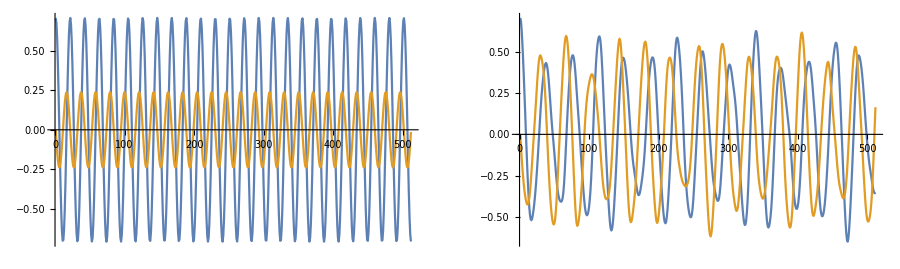

```mathematica
r1=ListPlot[{Re[a10],Im[a10]},Joined->True]; (* oscylator harmoniczny *)
r2=ListPlot[{Re[a102],Im[a102]},Joined->True]; (* oscylator kwadryczny *)
GraphicsGrid[{{r1,r2}},ImageSize->900]
```

### Spektrum wartości własnych oscylatora

```mathematica
spectrum=Abs[Fourier[a10]]^2; (* oscylator harmoniczny *)
spectrum2=Abs[Fourier[a102]]^2; (* oscylator kwadryczny *)
```

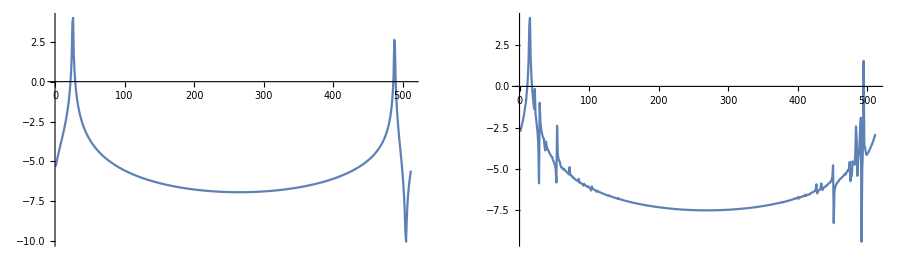

```mathematica
rys1=ListPlot[Log[spectrum],Joined->True,PlotRange->All]; (* oscylator harmoniczny *)
rys2=ListPlot[Log[spectrum2],Joined->True,PlotRange->All]; (* oscylator kwadryczny *)
GraphicsGrid[{{rys1,rys2}},ImageSize->900]
```

### Metoda wariacyjna dla oscylatora kwadrycznego

```mathematica
ψ=Exp[-α x^2/2]; (* próbna funkcja falowa z parametrem α *)
```

```mathematica
hamilt=-1/2 D[ψ,{x,2}]+g x^4 ψ; (* hamiltonian dla oscylatora kwadrycznego *)
```

```mathematica
norm=Simplify[∫_(-∞)^(+∞) Abs[ψ]^2ⅆx,α>0]; (* normalizacja próbnej funkcji falowej*)
```

```mathematica
eunorm=Simplify[∫_(-∞)^(+∞) ψ hamilt ψⅆx,α>0]; (* wartość energii dla nieunormowanej funkcji falowej *)
```

```mathematica
energy=eunorm/norm; (* energia wariacyjna w funkcji parametru α *)
```

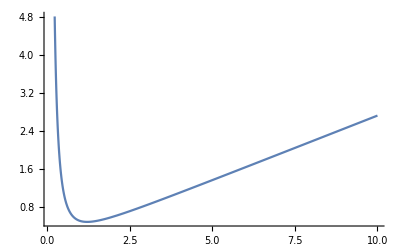

```mathematica
Plot[energy,{α,0.1,10}] (* zmiana wartości energii stanu podstawowego w funkcji α *)
```

```mathematica
FindMinimum[energy,{α,1.6}] (* szukanie parametru α minimalizującego energię stanu podstawowego *)
```

(0.493835
{α→1.20964})